```mathematica
(* Verified *)
CW[n_] := {{0, 0, 0,1, 0, 0}, {0, 0, 0,0,1, 0}, {0, 0, 0, 0 ,0, 1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0, 0}, {0, 0, -n^2, 0, 0,0}} ;
```

```mathematica
cmat[ab_, tau_, tf_] := MatrixExp[-(tau - tf) ab // Transpose][[4;;6, 1;;3]];
```

```mathematica
cmat[CW[5], 0.1, 1]  // MatrixForm
```

```mathematica
(*(100 (cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1])// MatrixForm*)


 (*100 (cmat[CW[5], 0.1, 1][[4;;6, 1;;3]] // Transpose).cmat[CW[5], 0.1, 1][[4;;6, 1;;3]].{0,0,1}*)

(*(deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt) /. {A -> CW[5], tf -> 1, delta -> {0,0,1}, Tmax -> 100, deltaT -> {{0,0,1}}, tau -> 0.1})[[1]]*)


100 (cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1].{0,0,1} / (({{0,0,1}}.(cmat[CW[5], 0.1, 1] // Transpose).cmat[CW[5], 0.1, 1].{0,0,1} // Sqrt)[[1]]);
```

```mathematica
xrf[tf_, delta_, h_, deltaT_, A_, n_, Rr_] := NIntegrate[  h n^2 Rr (cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta / (deltaT.(cmat[A, tau, tf] // Transpose).cmat[A, tau, tf].delta // Sqrt)[[1]]  ,{tau, 0, tf}];
```

```mathematica
x3fanalytical[tf_, h_, n_]:= h(2Floor[n tf / Pi]+1+ Mod[Floor[n tf / Pi], 2] Cos[n tf] - (Mod[Floor[n tf / Pi], 2] - 1)(- Cos[n tf]));
```

```mathematica
x3fanalytical[1,  100, 5] // N
```

```mathematica
xrf[1, {0, 0, 1}, 100, {{0,0,1}}, CW[5],5, 1] 
f[1, {0, 0, 1}, 100, {{0,0,1}}, CW[5],5, 1]
```

```mathematica
(* NSolve[x3fanalytical[t1, 100, 5] == 0, t1];
```

```mathematica
ContourPlot[x3fanalytical[t1, h1, 5] == 0, {t1, 0, 10}, {h1, 0, 100}];
```

```mathematica
Graphics3D[Point[SpherePoints[200]]];

columntorow[x_] := {x}
```

```mathematica
points = SpherePoints[1000];
points[[1]];
tfs = ConstantArray[1, 1000];
tfs[[1]];
hs = ConstantArray[100, 1000];
hs[[1]];
As = ConstantArray[CW[5], 1000];
As[[1]] // MatrixForm;
ns = ConstantArray[5, 1000];
ns[[1]];
Rrs = ConstantArray[1, 1000];
Rrs[[1]];
pointsT = columntorow /@ points;
pointsT[[1]] // MatrixForm;
(*{tfs, points, hs, pointsT, As, ns, Rrs}*)

rd = MapThread[xrf, {tfs, points, hs, pointsT, As, ns, Rrs}];
(*
Thread[f[tfs, points, hs, pointsT, As, ns, Rrs]];
in = {tfs, points, hs, pointsT, As, ns, Rrs} // Transpose;
xrf /@ in; *)
```

```mathematica
rdpoints = Map[Re, rd, {2}];
```

```mathematica
Graphics3D[Point[rdpoints]];
```

```mathematica
first2[x_] := {x[[1]], x[[2]]}
```

```mathematica
d2 = Map[first2, rdpoints];
Graphics[Point[d2]]
```

Polygon[…]

{{-1267.86,3417.98},{-1267.01,3269.1},{-1263.38,3547.56},{-1260.94,3118.76},{-1253.03,3649.13},{-1246.46,3685.47},{-1242.87,2738.83},{-1242.46,3702.83},{-1236.89,3726.28},{-1227.43,3754.23},{-1221.85,3767.94},{-1213.,3786.26},{-1203.85,3800.95},{-1198.53,3809.16},{-1189.37,3820.57},{-1189.22,2138.51},{-1183.51,3826.81},{-1174.,3836.2},{-1163.72,3844.25},{-1157.27,3848.98},{-1146.13,3855.81},{-1144.02,1716.06},{-1138.65,3859.38},{-1126.26,3865.15},{-1112.49,3869.74},{-1103.37,3872.18},{-1087.48,3875.49},{-1069.59,3877.21},{-1057.71,3878.05},{-1051.76,1030.65},{-1036.3,3877.59},{-1021.58,3876.08},{-995.288,3872.3},{-983.323,634.453},{-964.828,3864.69},{-943.67,3858.18},{-941.142,400.273},{-904.725,3843.16},{-877.22,3829.75},{-875.134,35.5857},{-858.736,3820.16},{-826.008,3802.02},{-764.589,3760.96},{-757.818,-490.008},{-720.377,3726.94},{-690.487,3701.12},{-684.621,-782.273},{-636.074,3653.18},{-575.217,3590.87},{-569.288,-1208.97},{-532.886,3545.42},{-456.908,3455.86},{-452.657,-1575.75},{-406.014,3387.89},{-386.119,-1780.17},{-371.783,3341.17},{-310.893,3256.75},{-279.347,-2071.74},{-204.213,3088.48},{-131.076,2962.05},{-119.203,-2460.56},{-26.1398,-2657.09},{1.07987,2712.53},{26.6327,-2764.78},{88.2396,2524.15},{106.598,-2919.12},{147.601,2393.18},{225.597,-3123.87},{247.762,2153.55},{292.369,-3227.31},{387.735,-3365.98},{420.518,1681.3},{472.752,-3474.14},{519.167,-3529.89},{532.704,1327.64},{587.116,-3604.38},{603.591,1082.06},{680.326,-3693.56},{722.491,641.004},{729.303,-3733.82},{756.674,-3754.5},{796.715,-3783.45},{837.189,130.981},{852.758,-3817.29},{882.701,-3832.82},{909.943,-212.745},{924.993,-3851.52},{947.787,-3859.08},{960.901,-3863.38},{980.626,-3869.04},{1008.91,-3874.6},{1019.64,-827.894},{1024.47,-3876.41},{1047.36,-3878.11},{1067.41,-3877.47},{1078.8,-3876.57},{1079.12,-1240.19},{1095.66,-3874.02},{1105.03,-3871.55},{1119.56,-3867.6},{1132.61,-3862.41},{1140.16,-3858.8},{1151.83,-3852.53},{1162.46,-3845.13},{1168.96,-3840.39},{1169.85,-1930.75},{1178.84,-3831.69},{1184.57,-3825.6},{1194.02,-3815.11},{1202.93,-3802.66},{1208.47,-3793.98},{1217.45,-3777.64},{1222.69,-3765.29},{1226.21,-3756.89},{1228.53,-2569.64},{1232.16,-3741.41},{1241.66,-3708.05},{1247.72,-3679.44},{1250.29,-2878.47},{1251.28,-3656.48},{1258.33,-3607.84},{1263.89,-3528.},{1266.2,-3204.86},{1267.31,-3450.27}}

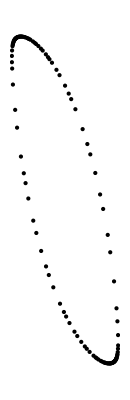

```mathematica
ConvexHullRegion[d2]
rdboundary = PolygonCoordinates[ConvexHullRegion[d2]]
Graphics[Point[rdboundary]]
```

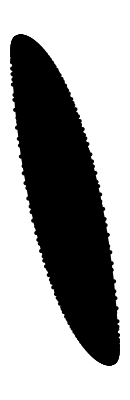

```mathematica
Region[ConvexHullRegion[d2],Epilog->{Black,Point[d2]}]
```